# Shifting polynomials

Here we generate polynomials in Z_p and look at how they change when shifted.

```mathematica
p=11; (* size of finite field *)

elements=Table[i,{i,0,p-1}];

numRoots=10; (* change as needed *)

roots=RandomSample[elements,numRoots]; (* random is not great for deep understanding, but for initial experiments it is ok *)

P[x_]=PolynomialMod[Expand[Product[(x-roots[[i]]),{i,1,Length[roots]}]],p];
```

This is our polynomial. Let’s see what shifts of this polynomial look like:

```mathematica
listOfShifts=Table[PolynomialMod[Expand[P[x+i]],p],{i,0,p-1}];
```

## These polynomials form an equivalence class. Give a proof. Moreover, there is a natural operation on polynomials on these equivalence classes, namely: If F and G are equivalence classes, F⋆G = {reduced(f×g): f∈F, g∈G} Where reduced(f×g) is the reduced polynomial corresponding to f×g. The set of these equivalence classes form a monoid under this operation.

```mathematica
Length[First[Sort[Table[Replace[CoefficientList[listOfShifts[[i]],x],0->Nothing,{1}],{i,1,Length[listOfShifts]}]]]]
```

2

This number represents the potential “savings” of using a polynomial to encode “numRoots.”

## Of the patterns of length p = 2,3,5,7,11, which “compress” to the polynomials with the most terms?

## Create a manipulate

2 x+4 x^2+3 x^3+x^4

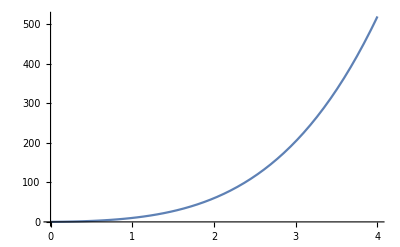

```mathematica
p=5;
roots={0,1,2,4};
P[x_]=PolynomialMod[Expand[Product[(x-roots[[i]]),{i,1,Length[roots]}]],p]
Plot[P[x],{x,0,4}]
```

```mathematica
Manipulate[
PolynomialMod[Expand[P[a x+b]],p],{a,1,4,1},{b,0,4,1}]
```